## Data for plots

```mathematica
od=({{0, 1, 1, 1, 1, 1}, {0, 0, 1, 1, 1, 1}, {0, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0}});
```

```mathematica
total=100000;
```

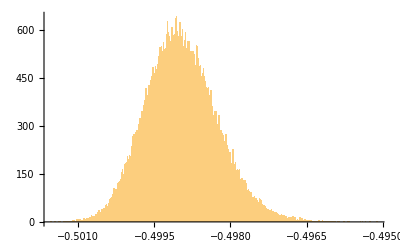

```mathematica
dataEPR={};
Monitor[
Do[
offdiagonal=od RandomReal[NormalDistribution[0,2 10^-5],{6,6}]+ⅈ od RandomReal[NormalDistribution[0,2 10^-5],{6,6}];
offdiagonal=offdiagonal+ConjugateTranspose[offdiagonal];

evals=Eigenvalues[DiagonalMatrix[{1,.5,.5,.5,.5,0}]+DiagonalMatrix[RandomReal[NormalDistribution[0,10^-3],{6}]]+offdiagonal];
AppendTo[dataEPR,evals⟦2⟧-1];

,{n,0,total}
]
,n]
Histogram[dataEPR,500]
```

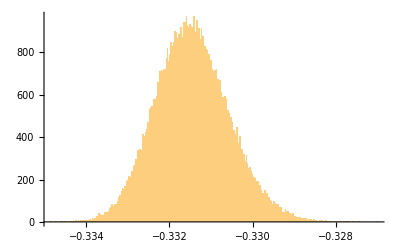

```mathematica
dataW={};
Monitor[
Do[
offdiagonal=od RandomReal[NormalDistribution[0,2 10^-5],{6,6}]+ⅈ od RandomReal[NormalDistribution[0,10^-3],{6,6}];
offdiagonal=offdiagonal+ConjugateTranspose[offdiagonal];

evals=Eigenvalues[DiagonalMatrix[{2/3,2/3,2/3,1/3,1/3,1/3}]+DiagonalMatrix[RandomReal[NormalDistribution[0,10^-3],{6}]]+offdiagonal];
AppendTo[dataW,evals⟦1⟧-1];

,{n,0,total}
]
,n]
Histogram[dataW,500]
```

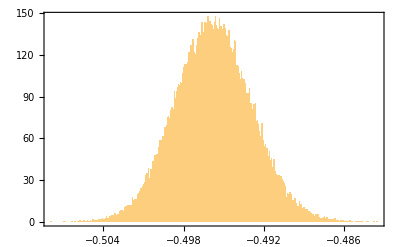

```mathematica
dataGHZ={};
Monitor[
Do[
offdiagonal=od RandomReal[NormalDistribution[0,2 10^-5],{6,6}]+ⅈ od RandomReal[NormalDistribution[0,2 10^-5],{6,6}];
offdiagonal=offdiagonal+ConjugateTranspose[offdiagonal];

evals=Eigenvalues[DiagonalMatrix[{.5,.5,.5,.5,.5,.5}]+DiagonalMatrix[RandomReal[NormalDistribution[0,2 10^-3],{6}]]+offdiagonal];
AppendTo[dataGHZ,evals⟦1⟧+evals⟦3⟧+evals⟦2⟧-2];

,{n,0,total}
]
,n]
Histogram[dataGHZ,500,"PDF",Frame->True]
```

## Plots for paper

```mathematica
<<MaTeX`
SetOptions[MaTeX,"FontSize"->12];
```

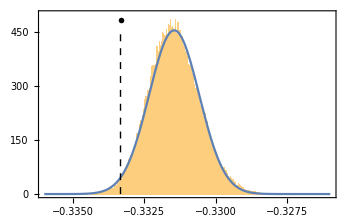

```mathematica
μ=Mean[dataW];
σ=StandardDeviation[dataW];
line1=Line[{{-1/3,0},{-1/3,450}}];
P2=Show[Histogram[dataW,500,"PDF",Frame->True,FrameLabel->{MaTeX["F_{\\mathrm{EPR}}"],MaTeX["\\rho(F_{\\mathrm{EPR}})"]},Epilog->{{Directive[{Black,Dashed}],line1},{Text[MaTeX["\\mu=-0.33146"],Scaled[{.77,.8}]],Text[MaTeX["\\sigma=+0.00088"],Scaled[{.77,.67}]],Text[MaTeX["\\mathrm{theoretical}\\ \\mathrm{value}"],{-1/3,485}]}},PlotRange->{{-.336,-.326},{0,500}},BaseStyle->{FontFamily->"LM Roman 12",FontSize->12},ImageSize->350,PlotLabel->MaTeX["\\textbf{(b) }|\\mathrm{W}\\rangle\\text{ violating }F_{\\mathrm{EPR}}\\geq 0"]],Plot[PDF[NormalDistribution[μ,σ]][x],{x,-.336,-.326},PlotRange->{{-.336,-.326},{0,500}}]]
```

-0.495777

0.00283992

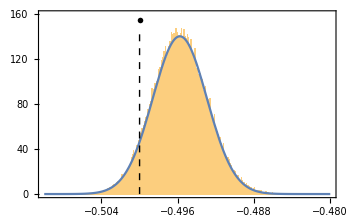

```mathematica
μ=Mean[dataGHZ]
σ=StandardDeviation[dataGHZ]
line1=Line[{{-.5,0},{-.5,145}}];P3=Show[Histogram[dataGHZ,500,"PDF",Frame->True,FrameLabel->{MaTeX["F_{\\mathrm{W}}"],MaTeX["\\rho(F_{\\mathrm{W}})"]},Epilog->{Directive[{Black,Dashed}],line1,{Text[MaTeX["\\mu=-0.49578"],Scaled[{.77,.8}]],Text[MaTeX["\\sigma=+0.00284"],Scaled[{.77,.67}]],Text[MaTeX["\\mathrm{theoretical}\\ \\mathrm{value}"],{-1/2,155}]}},PlotRange->{{-.51,-.48},{0,160}},BaseStyle->{FontFamily->"LM Roman 12",FontSize->12},ImageSize->350,PlotLabel->MaTeX["\\textbf{(c) }|\\mathrm{GHZ}\\rangle\\text{ violating }F_{\\mathrm{W}}\\geq 0"]],Plot[PDF[NormalDistribution[μ,σ]][x],{x,-.51,-.48},PlotRange->{{-.51,-.48},{0,160}}]]
```

-0.498967

0.000701401

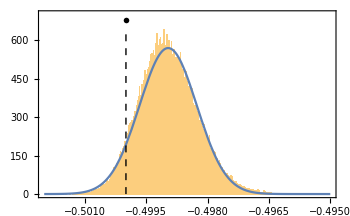

```mathematica
line1=Line[{{-.5,0},{-.5,630}}];
μ=Mean[dataEPR]
σ=StandardDeviation[dataEPR]
P1=Show[Histogram[dataEPR,500,"PDF",Frame->True,FrameLabel->{MaTeX["F_{\\mathrm{Slater}}"],MaTeX["\\rho(F_{\\mathrm{Slater}})"]},Epilog->{Directive[{Black,Dashed}],line1,{Text[MaTeX["\\mu=-0.49897"],Scaled[{.77,.8}]],Text[MaTeX["\\sigma=+0.00070"],Scaled[{.77,.67}]],Text[MaTeX["\\mathrm{theoretical}\\ \\mathrm{value}"],{-1/2,680}]}},PlotRange->{{-.502,-.495},{0,700}},ImageSize->350,BaseStyle->{FontFamily->"LM Roman 12",FontSize->12},PlotLabel->MaTeX["\\textbf{(a) }|\\mathrm{EPR}\\rangle\\text{ violating }F_{\\mathrm{Slater}}\\geq 0"]],Plot[PDF[NormalDistribution[μ,σ]][x],{x,-.502,-.495},PlotRange->{{-.502,-.495},{0,700}}]]
```

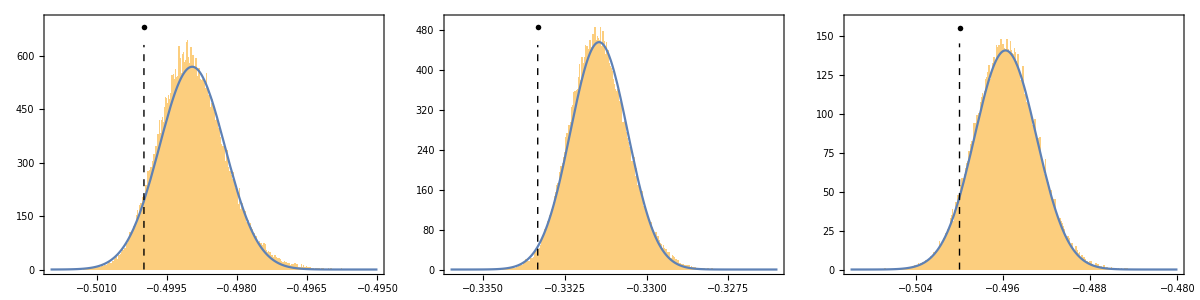

G:\My Drive\REPOSITORY\Research\Projects\O 2020- Investigating fermionicity in quantum dot systems\ErrorFigure.pdf

```mathematica
Plotf=Grid[{{P1,P2,P3}}]
Export[NotebookDirectory[]<>"ErrorFigure.pdf",Plotf]
```